```mathematica
$Assumptions={0<z,z<1,0<η,η<π/4};
D[1/b[η],{η,2}]/(1/b[η])==D[1/a[η],{η,2}]/(1/a[η])+k
%/.{a->Function[η,√Sin[2η]],k->1}//FullSimplify
%/.{b->Function[η,1/y[η]]}//FullSimplify
Inactive[DSolve][%,y,η]
DSolveChangeVariables[%,y,z,z==Sin[2 η]^2]//FullSimplify
Activate[%]
```

b[η] ((2 b'[η]^2)/b[η]^3-b''[η]/b[η]^2)==k+a[η] ((2 a'[η]^2)/a[η]^3-a''[η]/a[η]^2)

3 b[η] Csc[2 η]^2+b''[η]==(2 b'[η]^2)/b[η]

3 Csc[2 η]^2==y''[η]/y[η]

DSolve[3 Csc[2 η]^2==y''[η]/y[η],y,η]

DSolve[3+(8 z ((-1+2 z) y'[z]+2 (-1+z) z y''[z]))/y[z]==0,y,z]

{{y→Function[{z},(-1)^(3/4) z^(3/4) C[1] Hypergeometric2F1[3/4,3/4,2,z]+C[2] MeijerG[{{},{1,1}},{{-1/4,3/4},{}},z]]}}

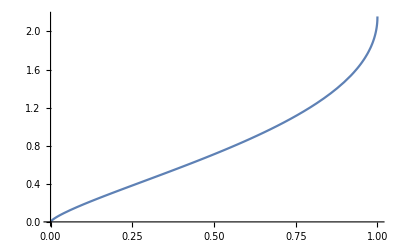

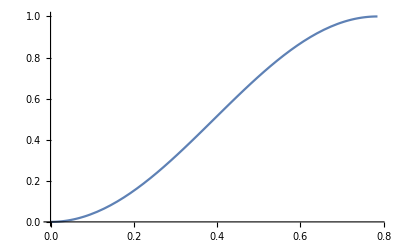

```mathematica
Plot[{z^(3/4) Hypergeometric2F1[3/4,3/4,2,z]},{z,0,1}]
Plot[Tanh[Log[Tan[π/4-η]]]^2,{η,0,π/4}]
```

```mathematica
$Assumptions={0<z,z<1,0<η,η<π/4};
z^(3/4) Hypergeometric2F1[3/4,3/4,2,z]//FunctionExpand//FullSimplify
%/.{z->Sin[2η]^2}//FullSimplify
```

1/(π z^(1/4))(16 EllipticE[1/2 (1-√(1-z))]-8 (1+√(1-z)) EllipticK[1/2 (1-√(1-z))])

1/(π √Sin[2 η])16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2])

```mathematica
MeijerG[{{},{1,1}},{{-1/4,3/4},{}},z]//FunctionExpand//FullSimplify
%/.{z->Sin[2η]^2}//FullSimplify
```

1/(π^2 z^(1/4))4 (-2 EllipticE[1/2 (1-√(1-z))]+2 EllipticE[1/2 (1+√(1-z))]+(1+√(1-z)) EllipticK[1/2 (1-√(1-z))]+(-1+√(1-z)) EllipticK[1/2 (1+√(1-z))]) Gamma[3/4]^2

(8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2))/(π^2 √Sin[2 η])

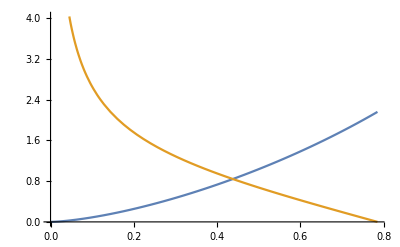

```mathematica
Plot[{(16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η])
,
1/(π^2 √Sin[2 η])8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2)},
{η,0,π/4}
]
```

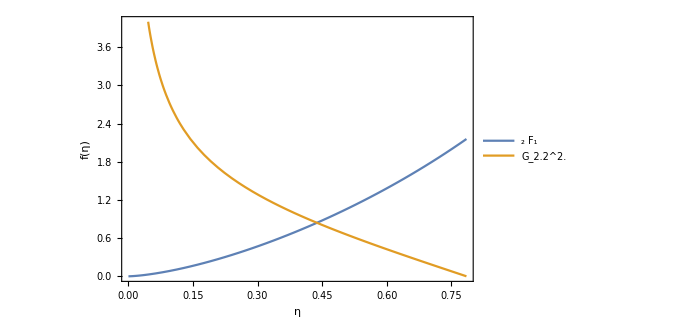

```mathematica
Show[Plot[{(16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η])
,
1/(π^2 √Sin[2 η])8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2)},
{η,0,π/4}, PlotRange->{{0,π/4},{0,4}},ImageSize->500, AspectRatio->2/3,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025], FontSize->20], FrameLabel->{Style["η", FontSize->32,FontFamily->"Times"],Style["f(η)",FontSize->24,FontFamily->"Times"]},PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["_2F_1",TeXForm,HoldForm]]],Text[Style[ToExpression["G^{2.0}_{2.2}",TeXForm,HoldForm]]]}, LabelStyle->Directive[FontSize->16],LegendFunction->(Framed[#1, FrameMargins->5,RoundingRadius->8,FrameStyle->Gray]&)],Scaled[{.275,.825}]]
]]
```

```mathematica
Manipulate[Plot[{1/(A((16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η]))+π^2/(8 Gamma[3/4]^2)1/(π^2 √Sin[2 η])8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2)),√Sin[2η]
},
{η,0,π/4}
],{{A,1},-1,5}]
```

```mathematica
1/(A(16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η])+π^2/(8 Gamma[3/4]^2)1/(π^2 √Sin[2 η])8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2)),{{c,1},0,5}
Solve[Limit[%/(√Sin[2η]),η->0]==1,B]
Limit[D[%,η]/D[√Sin[2η],η],η->0]
```

1/((16 A (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η])+(8 B Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2))/(π^2 √Sin[2 η]))

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{{B→π^2/(8 Gamma[3/4]^2)}}

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{{0}}

```mathematica
Series[1/(A(16 (EllipticE[Sin[η]^2]-Cos[η]^2 EllipticK[Sin[η]^2]))/(π √Sin[2 η])+π^2/(8 Gamma[3/4]^2)1/(π^2 √Sin[2 η])8 Gamma[3/4]^2 (EllipticE[Cos[η]^2]-EllipticE[Sin[η]^2]+Cos[η]^2 EllipticK[Sin[η]^2]-EllipticK[Cos[η]^2] Sin[η]^2)),{η,0,3}]
```

```mathematica
√2 √η+((-1-48 A+3 π+12 Log[2]-6 Log[η]) η^(5/2))/(6 √2)+O[η]^(7/2)
```

```mathematica
D[√2 √η+((-1-48 A+3 π+12 Log[2]-6 Log[η]) η^(5/2))/(6 √2),η]
```

1/(√2 √η)-η^(3/2)/(√2)+(5 η^(3/2) (-1-48 A+3 π+12 Log[2]-6 Log[η]))/(12 √2)